```mathematica
Clear[a]
```

```mathematica
encrypt[n_,string_]:=(
encryption=RandomInteger[{1,1000},{n,n}];
stringtrans=ToCharacterCode[string];
For[i=0,Mod[Length[stringtrans],n]≠ 0,i++,stringtrans=PadRight[ToCharacterCode[string],i+StringLength[string],32]];
stringtrans1=Transpose[Partition[stringtrans,n]];
estring=Transpose[Mod[encryption.(stringtrans1-32),97]+32];
estringtext=FromCharacterCode[Flatten[estring]];
mariokey=Import["http://img3.wikia.nocookie.net/__cb20130819015925/papermario/images/0/0c/Peach.jpg"];
Rasterize[mariokey];
squarekey=(Cases[InputForm[Rasterize[mariokey]],Raster[___],Infinity][[1,1]]);
squarekey1=squarekey;
replaceskey=Table[(squarekey[[85+i,85+j]]),{i,0,n-1},{j,0,n-1}];
replaceskey1=Flatten[replaceskey];
ethree=Table[3n1,{n1,1,n^2,1}];
replaceskey1[[ethree]]=Table[{Flatten[encryption][[i1]]},{i1,1,n^2,1}];
ereplace=Partition[Partition[Flatten[replaceskey1],3],n];
list=Table[n1,{n1,85,85+(n-1),1}];
For[i1=0,i1<n,i1++,(squarekey1[[85+i1,list]]=ereplace[[i1+1]])];
Graphics[Raster[squarekey1,{{0,0},{256,256}},{0,255},ColorFunction->RGBColor],ImageSize->Tiny]
estringtext
)
decrypt[s_,msg_,img_]:=(
eimg=(Cases[InputForm[img],Raster[___],Infinity][[1,1]]);
erkey=Table[(eimg[[85+i2,85+j2]]),{i2,0,s-1},{j2,0,s-1}];
encryption1=Partition[Flatten[erkey,1][[All,3]],s];
stringtrans2=Transpose[Partition[ToCharacterCode[msg],s]];
{g,{a,b}}=ExtendedGCD[Abs[Det[encryption1]],97];
dkey=Mod[Mod[a,97]*((Det[encryption1]/Abs[Det[encryption1]])*Det[encryption1]*Inverse[encryption1]),97];
txt=Transpose[Mod[dkey.(stringtrans2-32),97]+32];
FromCharacterCode[Flatten[txt]]
)
```

```mathematica
Clear[eimg,erkey]
```

```mathematica
encrypt[30,"I love you. <3"]
```

H/&=G|^oroc\/c^dXtP.x&.T8J1aYV -Graphics-

```mathematica
decrypt[30,"H/&=G|^oroc\\/c^dXtP.x&.T8J1aYV" ,-Graphics-]
```

I love you. <3

```mathematica
Length[encryption1]
```

15

```mathematica
Length[encryption]
```

15

```mathematica
Clear[p]
```

```mathematica
p[img_]:=(Cases[InputForm[img,Raster[___],Infinity]][[1,1]])
```

```mathematica
Cases[InputForm[-Graphics-],Raster[___],Infinity][[1,1]]-Cases[InputForm[ColorNegate[-Graphics-]],Raster[___],Infinity][[1,1]]
```

Part::partw: Part 1 of {} does not exist.

{{{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},243,{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧},{255-{}⟦1,1⟧,255-{}⟦1,1⟧,255-{}⟦1,1⟧}},254,{{1},254,{1}}}
 |  |  |  |

```mathematica
encryption//MatrixForm
```

(216 | 908 | 313 | 362 | 935 | 456 | 567 | 174 | 493 | 42 | 843 | 627 | 938 | 369 | 425 | 952 | 257 | 583 | 987 | 32 | 887 | 327 | 503 | 138 | 214 | 845 | 22 | 879 | 906 | 896
887 | 195 | 238 | 112 | 415 | 302 | 144 | 230 | 779 | 960 | 98 | 947 | 121 | 738 | 559 | 447 | 58 | 520 | 107 | 723 | 502 | 11 | 762 | 173 | 739 | 687 | 897 | 674 | 729 | 43
159 | 155 | 797 | 470 | 406 | 340 | 577 | 985 | 266 | 277 | 772 | 741 | 510 | 498 | 574 | 793 | 325 | 906 | 239 | 304 | 84 | 793 | 129 | 819 | 785 | 162 | 171 | 978 | 538 | 610
845 | 326 | 854 | 450 | 75 | 87 | 909 | 994 | 109 | 522 | 701 | 266 | 469 | 304 | 187 | 785 | 547 | 925 | 576 | 206 | 312 | 568 | 202 | 703 | 924 | 231 | 467 | 155 | 906 | 730
638 | 844 | 155 | 186 | 10 | 172 | 511 | 297 | 88 | 856 | 474 | 211 | 67 | 446 | 617 | 465 | 782 | 981 | 711 | 485 | 490 | 176 | 331 | 30 | 960 | 300 | 315 | 167 | 891 | 326
295 | 122 | 760 | 550 | 296 | 416 | 185 | 51 | 38 | 776 | 337 | 331 | 146 | 846 | 6 | 455 | 52 | 671 | 808 | 43 | 347 | 95 | 672 | 692 | 650 | 638 | 52 | 601 | 349 | 504
512 | 448 | 680 | 982 | 217 | 862 | 954 | 334 | 285 | 600 | 278 | 35 | 782 | 155 | 72 | 758 | 123 | 762 | 917 | 862 | 964 | 650 | 902 | 383 | 27 | 660 | 148 | 968 | 867 | 486
599 | 427 | 980 | 558 | 16 | 410 | 229 | 630 | 26 | 379 | 830 | 489 | 820 | 493 | 743 | 452 | 656 | 955 | 53 | 241 | 820 | 552 | 235 | 715 | 623 | 467 | 657 | 812 | 151 | 920
105 | 704 | 101 | 237 | 28 | 798 | 729 | 957 | 277 | 175 | 624 | 912 | 630 | 226 | 581 | 47 | 68 | 434 | 711 | 960 | 705 | 973 | 581 | 711 | 670 | 186 | 748 | 396 | 980 | 934
89 | 95 | 211 | 363 | 185 | 127 | 51 | 84 | 847 | 539 | 249 | 85 | 984 | 17 | 160 | 494 | 974 | 286 | 778 | 709 | 262 | 960 | 553 | 160 | 193 | 628 | 428 | 674 | 794 | 493
347 | 570 | 221 | 472 | 513 | 540 | 359 | 475 | 5 | 307 | 561 | 760 | 809 | 841 | 153 | 988 | 73 | 739 | 518 | 480 | 735 | 66 | 123 | 133 | 635 | 466 | 20 | 775 | 799 | 429
314 | 403 | 629 | 712 | 847 | 828 | 769 | 654 | 846 | 233 | 825 | 927 | 161 | 808 | 926 | 135 | 235 | 580 | 424 | 253 | 404 | 645 | 835 | 295 | 453 | 768 | 347 | 62 | 818 | 418
809 | 872 | 701 | 822 | 71 | 496 | 42 | 505 | 774 | 400 | 286 | 970 | 380 | 460 | 641 | 655 | 571 | 404 | 754 | 290 | 877 | 949 | 811 | 65 | 441 | 614 | 435 | 718 | 421 | 864
419 | 770 | 940 | 137 | 132 | 359 | 178 | 153 | 875 | 349 | 632 | 833 | 974 | 416 | 831 | 690 | 937 | 421 | 734 | 326 | 7 | 155 | 351 | 570 | 7 | 44 | 836 | 876 | 892 | 75
856 | 198 | 105 | 530 | 794 | 735 | 360 | 367 | 651 | 650 | 718 | 189 | 836 | 722 | 649 | 317 | 801 | 63 | 429 | 940 | 124 | 821 | 694 | 421 | 513 | 98 | 958 | 555 | 483 | 637
547 | 395 | 116 | 430 | 383 | 728 | 733 | 932 | 903 | 586 | 443 | 76 | 691 | 705 | 165 | 585 | 858 | 445 | 127 | 518 | 379 | 534 | 983 | 513 | 271 | 843 | 616 | 435 | 275 | 199
277 | 899 | 74 | 4 | 258 | 434 | 82 | 96 | 657 | 653 | 605 | 803 | 99 | 646 | 458 | 198 | 783 | 896 | 71 | 876 | 930 | 176 | 169 | 869 | 35 | 27 | 683 | 846 | 572 | 898
603 | 26 | 674 | 838 | 650 | 155 | 244 | 260 | 784 | 74 | 289 | 863 | 165 | 143 | 75 | 310 | 116 | 829 | 747 | 90 | 608 | 559 | 823 | 840 | 546 | 101 | 619 | 843 | 57 | 550
373 | 701 | 855 | 216 | 529 | 531 | 946 | 253 | 950 | 867 | 848 | 240 | 200 | 389 | 926 | 232 | 121 | 903 | 354 | 303 | 321 | 18 | 964 | 409 | 365 | 241 | 757 | 756 | 882 | 678
965 | 645 | 52 | 923 | 5 | 658 | 384 | 677 | 385 | 428 | 514 | 591 | 147 | 224 | 749 | 456 | 380 | 17 | 908 | 441 | 411 | 195 | 71 | 813 | 367 | 174 | 61 | 5 | 622 | 646
383 | 334 | 404 | 549 | 758 | 112 | 947 | 125 | 240 | 55 | 820 | 264 | 183 | 319 | 473 | 963 | 619 | 832 | 930 | 420 | 362 | 451 | 175 | 634 | 173 | 263 | 561 | 514 | 98 | 212
985 | 389 | 329 | 45 | 795 | 482 | 358 | 174 | 663 | 134 | 79 | 750 | 270 | 821 | 169 | 395 | 354 | 739 | 217 | 451 | 892 | 615 | 745 | 335 | 544 | 145 | 780 | 301 | 27 | 638
730 | 999 | 279 | 581 | 935 | 98 | 234 | 457 | 21 | 52 | 435 | 626 | 828 | 531 | 535 | 724 | 834 | 541 | 15 | 428 | 359 | 811 | 974 | 3 | 240 | 609 | 502 | 386 | 85 | 380
930 | 577 | 199 | 309 | 391 | 188 | 730 | 600 | 16 | 651 | 371 | 614 | 942 | 38 | 61 | 687 | 476 | 814 | 395 | 396 | 193 | 731 | 844 | 491 | 386 | 178 | 305 | 635 | 255 | 34
739 | 130 | 520 | 780 | 513 | 441 | 522 | 15 | 951 | 623 | 91 | 997 | 338 | 196 | 837 | 240 | 237 | 636 | 657 | 44 | 285 | 403 | 126 | 669 | 406 | 108 | 400 | 170 | 471 | 376
123 | 146 | 302 | 102 | 590 | 296 | 235 | 359 | 706 | 75 | 97 | 747 | 386 | 480 | 887 | 13 | 428 | 207 | 192 | 973 | 246 | 453 | 821 | 749 | 229 | 297 | 309 | 706 | 309 | 757
256 | 764 | 388 | 202 | 997 | 254 | 647 | 561 | 903 | 733 | 70 | 605 | 444 | 759 | 577 | 39 | 71 | 659 | 7 | 239 | 590 | 801 | 516 | 601 | 888 | 39 | 138 | 136 | 805 | 549
87 | 620 | 729 | 251 | 962 | 53 | 794 | 495 | 311 | 984 | 488 | 603 | 413 | 313 | 226 | 713 | 693 | 276 | 233 | 780 | 832 | 100 | 250 | 456 | 263 | 740 | 32 | 951 | 805 | 933
71 | 682 | 594 | 17 | 895 | 901 | 91 | 310 | 105 | 580 | 206 | 832 | 688 | 173 | 890 | 167 | 599 | 328 | 748 | 53 | 786 | 24 | 5 | 397 | 594 | 683 | 977 | 598 | 715 | 790
12 | 739 | 146 | 98 | 420 | 766 | 78 | 305 | 723 | 297 | 419 | 767 | 642 | 410 | 353 | 995 | 550 | 596 | 266 | 923 | 622 | 164 | 876 | 652 | 861 | 178 | 791 | 459 | 135 | 157)

```mathematica
p[-Graphics-]
```

-Graphics-

```mathematica
b=Table[(a[[85+i2,85+j2]]),{i2,0,15-1},{j2,0,15-1}];
Partition[Flatten[b,1][[All,3]],15]//MatrixForm
```

(303 | 487 | 279 | 155 | 466 | 41 | 79 | 283 | 237 | 188 | 241 | 395 | 483 | 159 | 58
340 | 408 | 104 | 273 | 467 | 462 | 314 | 248 | 432 | 324 | 174 | 94 | 165 | 74 | 82
213 | 479 | 171 | 270 | 141 | 85 | 46 | 425 | 141 | 66 | 26 | 245 | 68 | 123 | 159
274 | 381 | 102 | 95 | 102 | 396 | 288 | 139 | 311 | 90 | 330 | 403 | 212 | 222 | 448
77 | 469 | 153 | 201 | 362 | 72 | 466 | 72 | 401 | 86 | 271 | 94 | 468 | 99 | 175
68 | 401 | 466 | 475 | 216 | 130 | 141 | 355 | 388 | 424 | 218 | 27 | 468 | 424 | 34
378 | 304 | 315 | 401 | 107 | 62 | 402 | 174 | 41 | 219 | 47 | 460 | 120 | 73 | 417
26 | 149 | 62 | 281 | 372 | 111 | 110 | 56 | 218 | 134 | 206 | 118 | 456 | 32 | 266
370 | 467 | 442 | 277 | 64 | 174 | 171 | 121 | 490 | 400 | 75 | 107 | 417 | 330 | 382
48 | 205 | 462 | 131 | 102 | 468 | 407 | 66 | 459 | 402 | 165 | 391 | 101 | 294 | 491
218 | 282 | 362 | 4 | 383 | 137 | 199 | 100 | 174 | 229 | 244 | 118 | 309 | 472 | 489
14 | 49 | 314 | 115 | 6 | 434 | 395 | 261 | 204 | 224 | 403 | 150 | 43 | 425 | 89
13 | 477 | 209 | 464 | 7 | 327 | 177 | 362 | 304 | 138 | 404 | 163 | 8 | 396 | 356
19 | 476 | 253 | 293 | 352 | 65 | 382 | 41 | 427 | 264 | 431 | 171 | 228 | 251 | 446
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 15 | 14 | 15 | 15 | 15 | 15)

```mathematica
encryption//MatrixForm
```

(303 | 487 | 279 | 155 | 466 | 41 | 79 | 283 | 237 | 188 | 241 | 395 | 483 | 159 | 58
340 | 408 | 104 | 273 | 467 | 462 | 314 | 248 | 432 | 324 | 174 | 94 | 165 | 74 | 82
213 | 479 | 171 | 270 | 141 | 85 | 46 | 425 | 141 | 66 | 26 | 245 | 68 | 123 | 159
274 | 381 | 102 | 95 | 102 | 396 | 288 | 139 | 311 | 90 | 330 | 403 | 212 | 222 | 448
77 | 469 | 153 | 201 | 362 | 72 | 466 | 72 | 401 | 86 | 271 | 94 | 468 | 99 | 175
68 | 401 | 466 | 475 | 216 | 130 | 141 | 355 | 388 | 424 | 218 | 27 | 468 | 424 | 34
378 | 304 | 315 | 401 | 107 | 62 | 402 | 174 | 41 | 219 | 47 | 460 | 120 | 73 | 417
26 | 149 | 62 | 281 | 372 | 111 | 110 | 56 | 218 | 134 | 206 | 118 | 456 | 32 | 266
370 | 467 | 442 | 277 | 64 | 174 | 171 | 121 | 490 | 400 | 75 | 107 | 417 | 330 | 382
48 | 205 | 462 | 131 | 102 | 468 | 407 | 66 | 459 | 402 | 165 | 391 | 101 | 294 | 491
218 | 282 | 362 | 4 | 383 | 137 | 199 | 100 | 174 | 229 | 244 | 118 | 309 | 472 | 489
14 | 49 | 314 | 115 | 6 | 434 | 395 | 261 | 204 | 224 | 403 | 150 | 43 | 425 | 89
13 | 477 | 209 | 464 | 7 | 327 | 177 | 362 | 304 | 138 | 404 | 163 | 8 | 396 | 356
19 | 476 | 253 | 293 | 352 | 65 | 382 | 41 | 427 | 264 | 431 | 171 | 228 | 251 | 446
238 | 491 | 343 | 216 | 15 | 251 | 155 | 392 | 231 | 408 | 106 | 382 | 487 | 311 | 218)

```mathematica
f[-Graphics-]
```

{{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},218,{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},254,{1}}
 |  |  |  |

```mathematica
Cases[InputForm[-Graphics-,Raster[___],Infinity]]
```

-Graphics-

```mathematica
decrypt[15,"ZyTX%m:}T.80Wh,PF"]
```

Hello world!

```mathematica
encryption//MatrixForm
```

(376 | 160 | 268 | 117 | 272 | 9 | 6 | 74 | 100 | 211 | 61 | 416 | 218 | 252 | 330
27 | 288 | 320 | 489 | 478 | 423 | 234 | 235 | 21 | 455 | 132 | 263 | 32 | 147 | 66
459 | 115 | 210 | 492 | 221 | 104 | 353 | 83 | 467 | 232 | 477 | 222 | 219 | 366 | 258
292 | 76 | 497 | 192 | 446 | 349 | 216 | 349 | 148 | 424 | 287 | 441 | 174 | 472 | 260
101 | 299 | 261 | 492 | 238 | 173 | 95 | 346 | 273 | 443 | 211 | 398 | 101 | 287 | 156
218 | 213 | 296 | 144 | 97 | 63 | 383 | 12 | 149 | 114 | 34 | 314 | 429 | 205 | 262
401 | 266 | 82 | 327 | 361 | 495 | 19 | 39 | 174 | 356 | 332 | 452 | 352 | 432 | 350
183 | 165 | 3 | 238 | 475 | 385 | 273 | 253 | 457 | 380 | 338 | 245 | 482 | 455 | 267
478 | 390 | 108 | 3 | 280 | 292 | 321 | 323 | 349 | 481 | 410 | 262 | 6 | 317 | 105
412 | 314 | 18 | 254 | 385 | 315 | 120 | 373 | 89 | 181 | 310 | 415 | 50 | 249 | 173
105 | 385 | 379 | 457 | 196 | 50 | 378 | 300 | 184 | 192 | 289 | 177 | 321 | 236 | 260
475 | 173 | 475 | 286 | 175 | 82 | 154 | 360 | 451 | 123 | 274 | 194 | 360 | 311 | 115
356 | 193 | 186 | 158 | 149 | 144 | 393 | 379 | 185 | 469 | 237 | 291 | 361 | 232 | 385
133 | 250 | 331 | 213 | 50 | 12 | 54 | 253 | 359 | 23 | 264 | 466 | 398 | 173 | 188
191 | 360 | 130 | 256 | 50 | 75 | 255 | 497 | 87 | 90 | 497 | 42 | 128 | 473 | 248)

-Graphics-

```mathematica
256/3//N
```

85.3333

```mathematica
15^2/3//N
```

75.

```mathematica
Clear[squarekey]
```

```mathematica
squarekey=(Cases[InputForm[Rasterize[mariokey]],Raster[___],Infinity][[1,1]]);
squarekey1=squarekey;
```

```mathematica
replaceskey=Table[(squarekey[[85+i,85+j]]),{i,0,14},{j,0,14}];
```

```mathematica
replaceskey1=Flatten[replaceskey];
replaceskey1[[ethree]]=Table[{Flatten[encryption][[i1]]},{i1,1,75,1}];
ereplace=Partition[Partition[Flatten[replaceskey1],3],15];
```

```mathematica
n=15;
list=Table[n1,{n1,85,85+(n-1),1}];
For[i1=0,i1<14,i1++,(squarekey1[[85+i1,list]]=ereplace[[i1+1]])]
```

```mathematica
Graphics[Raster[squarekey1,{{0,0},{256,256}},{0,255},ColorFunction->RGBColor],ImageSize->200]
```

-Graphics-

```mathematica
squarekey1[[85,86]]
```

{75,75,160}

```mathematica
ereplace[[1]]
```

{{255,255,14},{75,75,241},{0,0,108},{0,0,425},{0,0,497},{1,4,348},{0,1,434},{0,0,182},{0,0,316},{1,1,293},{21,2,452},{81,8,266},{135,14,28},{175,18,199},{196,21,9}}

```mathematica
squarekey[[85,Table[n,{n,85,85+14,1}]]]
```

{{255,255,255},{75,75,75},{0,0,0},{0,0,0},{0,0,0},{1,4,8},{0,1,2},{0,0,0},{0,0,0},{1,1,1},{21,2,2},{81,8,6},{135,14,10},{175,18,13},{196,21,14}}

```mathematica
squarekey[[Table[n,{n,85,85+14,1}]]][[Table[n,{n,85,85+14,1}]]]//MatrixForm
```

Part::partw: Part {85, 86, 87, 88, 89, 90, 91, 92, 93, 94, 95, 96, 97, 98, 99} of {« 1 »} does not exist.

{{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},219,{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},13,{1}}⟦1⟧
 |  |  |  |

```mathematica
squarekey[[85,85]]
```

{255,255,255}

```mathematica
(Sequence@@part)
```

Sequence[{85,85},{86,85},{87,85},{88,85},{89,85},{90,85},{91,85},{92,85},{93,85},{94,85},{95,85},{96,85},{97,85},{98,85},{99,85},{85,86},{86,86},{87,86},{88,86},{89,86},{90,86},{91,86},{92,86},{93,86},{94,86},{95,86},{96,86},{97,86},{98,86},{99,86},{85,87},{86,87},{87,87},{88,87},{89,87},{90,87},{91,87},{92,87},{93,87},{94,87},{95,87},{96,87},{97,87},{98,87},{99,87},{85,88},{86,88},{87,88},{88,88},{89,88},{90,88},{91,88},{92,88},{93,88},{94,88},{95,88},{96,88},{97,88},{98,88},{99,88},{85,89},{86,89},{87,89},{88,89},{89,89},{90,89},{91,89},{92,89},{93,89},{94,89},{95,89},{96,89},{97,89},{98,89},{99,89},{85,90},{86,90},{87,90},{88,90},{89,90},{90,90},{91,90},{92,90},{93,90},{94,90},{95,90},{96,90},{97,90},{98,90},{99,90},{85,91},{86,91},{87,91},{88,91},{89,91},{90,91},{91,91},{92,91},{93,91},{94,91},{95,91},{96,91},{97,91},{98,91},{99,91},{85,92},{86,92},{87,92},{88,92},{89,92},{90,92},{91,92},{92,92},{93,92},{94,92},{95,92},{96,92},{97,92},{98,92},{99,92},{85,93},{86,93},{87,93},{88,93},{89,93},{90,93},{91,93},{92,93},{93,93},{94,93},{95,93},{96,93},{97,93},{98,93},{99,93},{85,94},{86,94},{87,94},{88,94},{89,94},{90,94},{91,94},{92,94},{93,94},{94,94},{95,94},{96,94},{97,94},{98,94},{99,94},{85,95},{86,95},{87,95},{88,95},{89,95},{90,95},{91,95},{92,95},{93,95},{94,95},{95,95},{96,95},{97,95},{98,95},{99,95},{85,96},{86,96},{87,96},{88,96},{89,96},{90,96},{91,96},{92,96},{93,96},{94,96},{95,96},{96,96},{97,96},{98,96},{99,96},{85,97},{86,97},{87,97},{88,97},{89,97},{90,97},{91,97},{92,97},{93,97},{94,97},{95,97},{96,97},{97,97},{98,97},{99,97},{85,98},{86,98},{87,98},{88,98},{89,98},{90,98},{91,98},{92,98},{93,98},{94,98},{95,98},{96,98},{97,98},{98,98},{99,98},{85,99},{86,99},{87,99},{88,99},{89,99},{90,99},{91,99},{92,99},{93,99},{94,99},{95,99},{96,99},{97,99},{98,99},{99,99}]

```mathematica
Partition[StringReplace[ToString[part],{"{"->"","}"->""}],2]
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

Partition[85, 85, 86, 85, 87, 85, 88, 85, 89, 85, 90, 85, 91, 85, 92, 85, 93, 85, 94, 85, 95, 85, 96, 85, 97, 85, 98, 85, 99, 85, 85, 86, 86, 86, 87, 86, 88, 86, 89, 86, 90, 86, 91, 86, 92, 86, 93, 86, 94, 86, 95, 86, 96, 86, 97, 86, 98, 86, 99, 86, 85, 87, 86, 87, 87, 87, 88, 87, 89, 87, 90, 87, 91, 87, 92, 87, 93, 87, 94, 87, 95, 87, 96, 87, 97, 87, 98, 87, 99, 87, 85, 88, 86, 88, 87, 88, 88, 88, 89, 88, 90, 88, 91, 88, 92, 88, 93, 88, 94, 88, 95, 88, 96, 88, 97, 88, 98, 88, 99, 88, 85, 89, 86, 89, 87, 89, 88, 89, 89, 89, 90, 89, 91, 89, 92, 89, 93, 89, 94, 89, 95, 89, 96, 89, 97, 89, 98, 89, 99, 89, 85, 90, 86, 90, 87, 90, 88, 90, 89, 90, 90, 90, 91, 90, 92, 90, 93, 90, 94, 90, 95, 90, 96, 90, 97, 90, 98, 90, 99, 90, 85, 91, 86, 91, 87, 91, 88, 91, 89, 91, 90, 91, 91, 91, 92, 91, 93, 91, 94, 91, 95, 91, 96, 91, 97, 91, 98, 91, 99, 91, 85, 92, 86, 92, 87, 92, 88, 92, 89, 92, 90, 92, 91, 92, 92, 92, 93, 92, 94, 92, 95, 92, 96, 92, 97, 92, 98, 92, 99, 92, 85, 93, 86, 93, 87, 93, 88, 93, 89, 93, 90, 93, 91, 93, 92, 93, 93, 93, 94, 93, 95, 93, 96, 93, 97, 93, 98, 93, 99, 93, 85, 94, 86, 94, 87, 94, 88, 94, 89, 94, 90, 94, 91, 94, 92, 94, 93, 94, 94, 94, 95, 94, 96, 94, 97, 94, 98, 94, 99, 94, 85, 95, 86, 95, 87, 95, 88, 95, 89, 95, 90, 95, 91, 95, 92, 95, 93, 95, 94, 95, 95, 95, 96, 95, 97, 95, 98, 95, 99, 95, 85, 96, 86, 96, 87, 96, 88, 96, 89, 96, 90, 96, 91, 96, 92, 96, 93, 96, 94, 96, 95, 96, 96, 96, 97, 96, 98, 96, 99, 96, 85, 97, 86, 97, 87, 97, 88, 97, 89, 97, 90, 97, 91, 97, 92, 97, 93, 97, 94, 97, 95, 97, 96, 97, 97, 97, 98, 97, 99, 97, 85, 98, 86, 98, 87, 98, 88, 98, 89, 98, 90, 98, 91, 98, 92, 98, 93, 98, 94, 98, 95, 98, 96, 98, 97, 98, 98, 98, 99, 98, 85, 99, 86, 99, 87, 99, 88, 99, 89, 99, 90, 99, 91, 99, 92, 99, 93, 99, 94, 99, 95, 99, 96, 99, 97, 99, 98, 99, 99, 99,2]

```mathematica
ereplace[[1]]
```

Part::partd: Part specification ereplace ⟦ 1 ⟧ is longer than depth of object.

ereplace⟦1⟧

```mathematica
ReplacePart[squarekey,{85,85}->ereplace[[1]]]
```

Part::partd: Part specification ereplace ⟦ 1 ⟧ is longer than depth of object.

{{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},218,{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},254,{1}}
 |  |  |  |

```mathematica
squarekey[[85,85]]
```

{255,255,255}

```mathematica
part[[1]]
```

{85,85}

```mathematica
Length[squarekey]
```

256

```mathematica
squarekey[[85,85]]
```

{255,255,255}

```mathematica
Table[ereplace[[i1]],{i1,1,225}][[1]]
```

Part::partd: Part specification ereplace ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification ereplace ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification ereplace ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ereplace⟦1⟧

```mathematica
ereplace[[1]]
```

$Aborted

```mathematica
squarekey[[{85,85}]]
```

{{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{251,251,251},{134,134,134},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{58,58,58},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{120,120,120},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{110,110,110},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{236,236,236},{36,36,36},{0,0,0},{0,0,0},{172,172,172},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{254,254,254},{253,253,253},{253,253,253},{252,252,252},{250,251,250},{249,249,249},{247,248,247},{245,247,246},{243,244,244},{241,242,241},{242,242,242},{253,253,253},{255,255,255},{255,255,255},{75,75,75},{0,0,0},{0,0,0},{0,0,0},{1,4,8},{0,1,2},{0,0,0},{0,0,0},{1,1,1},{21,2,2},{81,8,6},{135,14,10},{175,18,13},{196,21,14},{210,23,15},{213,25,16},{216,27,17},{217,27,15},{208,27,14},{190,26,12},{151,22,10},{91,14,6},{25,4,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{5,30,67},{12,76,171},{12,77,174},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{13,79,179},{4,29,65},{0,0,0},{0,0,0},{25,23,5},{236,225,53},{255,246,60},{248,220,45},{240,200,32},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{255,215,36},{91,77,13},{0,0,0},{0,0,0},{7,44,99},{13,79,180},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{13,80,180},{6,37,84},{0,0,0},{0,0,0},{0,0,0},{62,58,11},{52,49,10},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{7,3,1},{111,49,9},{127,56,10},{125,55,10},{125,55,10},{126,55,10},{126,55,10},{126,55,11},{126,55,12},{126,55,12},{126,55,12},{127,56,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{129,57,12},{129,58,12},{130,58,12},{130,59,12},{139,63,13},{81,37,8},{0,0,0},{0,0,0},{90,90,90},{255,255,255},{255,255,255},{255,255,255},{174,174,174},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{101,101,101},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{251,251,251},{134,134,134},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{58,58,58},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{120,120,120},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{110,110,110},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{236,236,236},{36,36,36},{0,0,0},{0,0,0},{172,172,172},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{254,254,254},{253,253,253},{253,253,253},{252,252,252},{250,251,250},{249,249,249},{247,248,247},{245,247,246},{243,244,244},{241,242,241},{242,242,242},{253,253,253},{255,255,255},{255,255,255},{75,75,75},{0,0,0},{0,0,0},{0,0,0},{1,4,8},{0,1,2},{0,0,0},{0,0,0},{1,1,1},{21,2,2},{81,8,6},{135,14,10},{175,18,13},{196,21,14},{210,23,15},{213,25,16},{216,27,17},{217,27,15},{208,27,14},{190,26,12},{151,22,10},{91,14,6},{25,4,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{5,30,67},{12,76,171},{12,77,174},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{13,79,179},{4,29,65},{0,0,0},{0,0,0},{25,23,5},{236,225,53},{255,246,60},{248,220,45},{240,200,32},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{241,203,34},{255,215,36},{91,77,13},{0,0,0},{0,0,0},{7,44,99},{13,79,180},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{12,75,170},{13,80,180},{6,37,84},{0,0,0},{0,0,0},{0,0,0},{62,58,11},{52,49,10},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{7,3,1},{111,49,9},{127,56,10},{125,55,10},{125,55,10},{126,55,10},{126,55,10},{126,55,11},{126,55,12},{126,55,12},{126,55,12},{127,56,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{128,57,12},{129,57,12},{129,58,12},{130,58,12},{130,59,12},{139,63,13},{81,37,8},{0,0,0},{0,0,0},{90,90,90},{255,255,255},{255,255,255},{255,255,255},{174,174,174},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{101,101,101},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}}}

```mathematica
squarekey[[part[[1]]]]=ereplace[[1]]
```

{255,255,113}

```mathematica
squarekey[[85,85]]
```

{255,255,255}

```mathematica
replaceskey//MatrixForm
```

((255
255
255) | (75
75
75) | (0
0
0) | (0
0
0) | (0
0
0) | (1
4
8) | (0
1
2) | (0
0
0) | (0
0
0) | (1
1
1) | (21
2
2) | (81
8
6) | (135
14
10) | (175
18
13) | (196
21
14)
(194
194
194) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (37
5
4) | (131
16
12) | (197
20
14) | (219
22
16) | (219
22
16) | (215
22
15) | (212
22
15)
(70
70
70) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (9
1
1) | (113
12
8) | (207
22
15) | (220
22
16) | (211
21
15) | (207
21
15) | (207
21
15) | (207
22
15) | (207
22
15)
(0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (26
5
1) | (186
31
11) | (227
26
16) | (209
22
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
22
15) | (207
22
15)
(0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (20
3
1) | (200
34
11) | (255
46
15) | (222
30
15) | (205
20
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
22
15)
(0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (67
12
4) | (255
44
15) | (245
43
14) | (235
37
14) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15)
(12
12
12) | (0
0
0) | (0
0
0) | (0
0
0) | (4
1
0) | (200
35
12) | (252
44
14) | (243
42
14) | (214
26
15) | (206
20
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15)
(53
53
53) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (105
18
6) | (255
45
15) | (245
43
14) | (227
33
15) | (205
20
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15)
(64
64
64) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (24
4
1) | (226
39
13) | (249
43
14) | (239
40
14) | (209
22
15) | (206
21
15) | (207
21
15) | (209
29
23) | (207
21
15) | (207
21
15)
(47
47
47) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (143
25
8) | (255
45
15) | (245
43
14) | (220
28
15) | (205
20
15) | (207
21
15) | (207
22
16) | (207
21
15) | (207
21
15)
(12
12
12) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (50
9
3) | (243
42
14) | (247
43
14) | (233
36
14) | (206
20
15) | (207
21
15) | (207
21
15) | (207
21
15) | (207
21
15)
(0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (178
31
10) | (255
44
15) | (242
42
14) | (212
24
15) | (206
20
15) | (207
21
15) | (207
21
15) | (207
21
15)
(0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (82
14
5) | (254
44
15) | (246
43
14) | (225
32
15) | (205
20
15) | (207
21
15) | (207
21
15) | (207
21
15)
(0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (9
2
0) | (209
36
12) | (252
44
14) | (238
39
14) | (208
21
15) | (207
21
15) | (207
21
15) | (207
21
15)
(0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (0
0
0) | (118
20
6) | (255
45
15) | (244
43
14) | (217
27
15) | (205
20
15) | (207
21
15) | (207
21
15))

```mathematica
Table[(ReplacePart[replaceskey,{1+i1,1+j1,3}->encryption[[i1,j1]]]),{i1,1,15,1},{j1,1,15,1}]
```

{1}
 |  |  |  |

```mathematica
Flatten[encryption]
```

{113,310,422,29,6,348,202,188,117,301,101,279,350,251,143,392,25,392,333,88,295,165,93,245,448,427,413,416,369,145,349,36,18,158,436,280,305,146,168,106,291,487,179,48,265,423,427,493,89,39,479,21,206,353,419,490,291,143,395,465,36,273,379,118,87,117,385,110,437,432,145,35,459,267,87,406,158,272,360,184,147,54,468,62,31,311,272,247,368,424,320,292,116,434,256,250,109,368,497,212,174,413,172,410,114,162,78,165,429,143,416,267,289,65,452,15,353,413,477,387,23,392,121,189,486,72,211,256,303,348,446,415,321,72,383,71,428,363,325,104,347,185,209,495,458,15,280,44,78,268,74,447,52,331,204,133,379,495,346,306,421,414,76,208,50,244,165,248,300,239,425,197,302,341,314,297,108,473,104,97,144,122,108,195,381,335,216,455,192,157,303,458,282,368,27,237,264,207,487,443,274,202,170,468,193,186,120,350,200,413,143,21,134,334,437,141,167,51,493,441,454,128,164,73,44}

{3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99,102,105,108,111,114,117,120,123,126,129,132,135,138,141,144,147,150,153,156,159,162,165,168,171,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,225}

```mathematica
replaceskey
```

{{{255,255,255},{75,75,75},{0,0,0},{0,0,0},{0,0,0},{1,4,8},{0,1,2},{0,0,0},{0,0,0},{1,1,1},{21,2,2},{81,8,6},{135,14,10},{175,18,13},{196,21,14}},{{194,194,194},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{37,5,4},{131,16,12},{197,20,14},{219,22,16},{219,22,16},{215,22,15},{212,22,15}},{{70,70,70},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{9,1,1},{113,12,8},{207,22,15},{220,22,16},{211,21,15},{207,21,15},{207,21,15},{207,22,15},{207,22,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{26,5,1},{186,31,11},{227,26,16},{209,22,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,22,15},{207,22,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{20,3,1},{200,34,11},{255,46,15},{222,30,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,22,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{67,12,4},{255,44,15},{245,43,14},{235,37,14},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{12,12,12},{0,0,0},{0,0,0},{0,0,0},{4,1,0},{200,35,12},{252,44,14},{243,42,14},{214,26,15},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{53,53,53},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{105,18,6},{255,45,15},{245,43,14},{227,33,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{64,64,64},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{24,4,1},{226,39,13},{249,43,14},{239,40,14},{209,22,15},{206,21,15},{207,21,15},{209,29,23},{207,21,15},{207,21,15}},{{47,47,47},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{143,25,8},{255,45,15},{245,43,14},{220,28,15},{205,20,15},{207,21,15},{207,22,16},{207,21,15},{207,21,15}},{{12,12,12},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{50,9,3},{243,42,14},{247,43,14},{233,36,14},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{178,31,10},{255,44,15},{242,42,14},{212,24,15},{206,20,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{82,14,5},{254,44,15},{246,43,14},{225,32,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{9,2,0},{209,36,12},{252,44,14},{238,39,14},{208,21,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{118,20,6},{255,45,15},{244,43,14},{217,27,15},{205,20,15},{207,21,15},{207,21,15}}}

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[ereplace].

Flatten[ereplace]

```mathematica
225/3//N
```

75.

```mathematica
Partition[replaceskey1,3]
```

{{255,255,255},{75,75,75},{0,0,0},{0,0,0},{0,0,0},{1,4,8},{0,1,2},{0,0,0},{0,0,0},{1,1,1},{21,2,2},{81,8,6},{135,14,10},{175,18,13},{196,21,14},{194,194,194},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{37,5,4},{131,16,12},{197,20,14},{219,22,16},{219,22,16},{215,22,15},{212,22,15},{70,70,70},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{9,1,1},{113,12,8},{207,22,15},{220,22,16},{211,21,15},{207,21,15},{207,21,15},{207,22,15},{207,22,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{26,5,1},{186,31,11},{227,26,16},{209,22,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,22,15},{207,22,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{20,3,1},{200,34,11},{255,46,15},{222,30,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,22,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{67,12,4},{255,44,15},{245,43,14},{235,37,14},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{12,12,12},{0,0,0},{0,0,0},{0,0,0},{4,1,0},{200,35,12},{252,44,14},{243,42,14},{214,26,15},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{53,53,53},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{105,18,6},{255,45,15},{245,43,14},{227,33,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{64,64,64},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{24,4,1},{226,39,13},{249,43,14},{239,40,14},{209,22,15},{206,21,15},{207,21,15},{209,29,23},{207,21,15},{207,21,15},{47,47,47},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{143,25,8},{255,45,15},{245,43,14},{220,28,15},{205,20,15},{207,21,15},{207,22,16},{207,21,15},{207,21,15},{12,12,12},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{50,9,3},{243,42,14},{247,43,14},{233,36,14},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{178,31,10},{255,44,15},{242,42,14},{212,24,15},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{82,14,5},{254,44,15},{246,43,14},{225,32,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{9,2,0},{209,36,12},{252,44,14},{238,39,14},{208,21,15},{207,21,15},{207,21,15},{207,21,15},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{118,20,6},{255,45,15},{244,43,14},{217,27,15},{205,20,15},{207,21,15},{207,21,15}}

```mathematica
ReplacePart[Flatten[replaceskey],{ethree->67}]
```

{255,255,255,75,75,75,0,0,0,0,0,0,0,0,0,1,4,8,0,1,2,0,0,0,0,0,0,1,1,1,21,2,2,81,8,6,135,14,10,175,18,13,196,21,14,194,194,194,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,37,5,4,131,16,12,197,20,14,219,22,16,219,22,16,215,22,15,212,22,15,70,70,70,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9,1,1,113,12,8,207,22,15,220,22,16,211,21,15,207,21,15,207,21,15,207,22,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,26,5,1,186,31,11,227,26,16,209,22,15,207,21,15,207,21,15,207,21,15,207,21,15,207,22,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,20,3,1,200,34,11,255,46,15,222,30,15,205,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,67,12,4,255,44,15,245,43,14,235,37,14,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,12,12,12,0,0,0,0,0,0,0,0,0,4,1,0,200,35,12,252,44,14,243,42,14,214,26,15,206,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,53,53,53,0,0,0,0,0,0,0,0,0,0,0,0,105,18,6,255,45,15,245,43,14,227,33,15,205,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,64,64,64,0,0,0,0,0,0,0,0,0,0,0,0,24,4,1,226,39,13,249,43,14,239,40,14,209,22,15,206,21,15,207,21,15,209,29,23,207,21,15,207,21,15,47,47,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,143,25,8,255,45,15,245,43,14,220,28,15,205,20,15,207,21,15,207,22,16,207,21,15,207,21,15,12,12,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50,9,3,243,42,14,247,43,14,233,36,14,206,20,15,207,21,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,178,31,10,255,44,15,242,42,14,212,24,15,206,20,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,82,14,5,254,44,15,246,43,14,225,32,15,205,20,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9,2,0,209,36,12,252,44,14,238,39,14,208,21,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,118,20,6,255,45,15,244,43,14,217,27,15,205,20,15,207,21,15,207,21,15}

```mathematica
ReplacePart[Flatten[replaceskey],{3p_}->67]
```

{255,255,255,75,75,75,0,0,0,0,0,0,0,0,0,1,4,8,0,1,2,0,0,0,0,0,0,1,1,1,21,2,2,81,8,6,135,14,10,175,18,13,196,21,14,194,194,194,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,37,5,4,131,16,12,197,20,14,219,22,16,219,22,16,215,22,15,212,22,15,70,70,70,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9,1,1,113,12,8,207,22,15,220,22,16,211,21,15,207,21,15,207,21,15,207,22,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,26,5,1,186,31,11,227,26,16,209,22,15,207,21,15,207,21,15,207,21,15,207,21,15,207,22,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,20,3,1,200,34,11,255,46,15,222,30,15,205,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,22,15,0,0,0,0,0,0,0,0,0,0,0,0,67,12,4,255,44,15,245,43,14,235,37,14,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,12,12,12,0,0,0,0,0,0,0,0,0,4,1,0,200,35,12,252,44,14,243,42,14,214,26,15,206,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,53,53,53,0,0,0,0,0,0,0,0,0,0,0,0,105,18,6,255,45,15,245,43,14,227,33,15,205,20,15,207,21,15,207,21,15,207,21,15,207,21,15,207,21,15,64,64,64,0,0,0,0,0,0,0,0,0,0,0,0,24,4,1,226,39,13,249,43,14,239,40,14,209,22,15,206,21,15,207,21,15,209,29,23,207,21,15,207,21,15,47,47,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,143,25,8,255,45,15,245,43,14,220,28,15,205,20,15,207,21,15,207,22,16,207,21,15,207,21,15,12,12,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50,9,3,243,42,14,247,43,14,233,36,14,206,20,15,207,21,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,178,31,10,255,44,15,242,42,14,212,24,15,206,20,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,82,14,5,254,44,15,246,43,14,225,32,15,205,20,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,9,2,0,209,36,12,252,44,14,238,39,14,208,21,15,207,21,15,207,21,15,207,21,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,118,20,6,255,45,15,244,43,14,217,27,15,205,20,15,207,21,15,207,21,15}

```mathematica
replaceskey
```

{{{255,255,255},{75,75,75},{0,0,0},{0,0,0},{0,0,0},{1,4,8},{0,1,2},{0,0,0},{0,0,0},{1,1,1},{21,2,2},{81,8,6},{135,14,10},{175,18,13},{196,21,14}},{{194,194,194},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{37,5,4},{131,16,12},{197,20,14},{219,22,16},{219,22,16},{215,22,15},{212,22,15}},{{70,70,70},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{9,1,1},{113,12,8},{207,22,15},{220,22,16},{211,21,15},{207,21,15},{207,21,15},{207,22,15},{207,22,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{26,5,1},{186,31,11},{227,26,16},{209,22,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,22,15},{207,22,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{20,3,1},{200,34,11},{255,46,15},{222,30,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,22,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{67,12,4},{255,44,15},{245,43,14},{235,37,14},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{12,12,12},{0,0,0},{0,0,0},{0,0,0},{4,1,0},{200,35,12},{252,44,14},{243,42,14},{214,26,15},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{53,53,53},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{105,18,6},{255,45,15},{245,43,14},{227,33,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{64,64,64},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{24,4,1},{226,39,13},{249,43,14},{239,40,14},{209,22,15},{206,21,15},{207,21,15},{209,29,23},{207,21,15},{207,21,15}},{{47,47,47},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{143,25,8},{255,45,15},{245,43,14},{220,28,15},{205,20,15},{207,21,15},{207,22,16},{207,21,15},{207,21,15}},{{12,12,12},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{50,9,3},{243,42,14},{247,43,14},{233,36,14},{206,20,15},{207,21,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{178,31,10},{255,44,15},{242,42,14},{212,24,15},{206,20,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{82,14,5},{254,44,15},{246,43,14},{225,32,15},{205,20,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{9,2,0},{209,36,12},{252,44,14},{238,39,14},{208,21,15},{207,21,15},{207,21,15},{207,21,15}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{118,20,6},{255,45,15},{244,43,14},{217,27,15},{205,20,15},{207,21,15},{207,21,15}}}

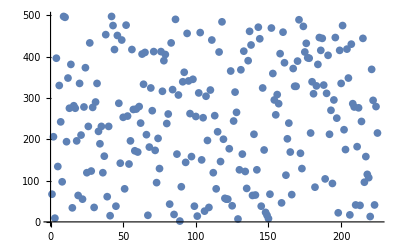
```mathematica
Partition[(Cases[InputForm[-Graphics-],Point[___],Infinity][[1,1]])[[All,2]],15]//MatrixForm
```

(67. | 206. | 9. | 396. | 134. | 330. | 242. | 97. | 497. | 495. | 194. | 348. | 275. | 381. | 34.
281. | 275. | 196. | 64. | 335. | 210. | 55. | 278. | 373. | 119. | 231. | 433. | 123. | 277. | 35.
290. | 335. | 219. | 189. | 231. | 119. | 159. | 453. | 61. | 231. | 15. | 497. | 475. | 417. | 38.
451. | 287. | 142. | 440. | 253. | 80. | 476. | 256. | 140. | 196. | 417. | 272. | 172. | 273. | 169.
279. | 239. | 406. | 333. | 410. | 211. | 16. | 181. | 324. | 269. | 412. | 173. | 95. | 202. | 129.
412. | 316. | 390. | 405. | 238. | 261. | 43. | 433. | 320. | 18. | 490. | 164. | 307. | 2. | 85.
339. | 362. | 144. | 456. | 341. | 262. | 158. | 345. | 38. | 255. | 14. | 312. | 458. | 150. | 252.
26. | 304. | 197. | 35. | 319. | 440. | 119. | 257. | 80. | 218. | 411. | 146. | 484. | 200. | 57.
55. | 55. | 177. | 365. | 39. | 244. | 314. | 265. | 7. | 126. | 368. | 164. | 413. | 122. | 81.
390. | 461. | 428. | 64. | 212. | 65. | 126. | 471. | 443. | 38. | 324. | 174. | 23. | 16. | 8.
67. | 469. | 359. | 295. | 259. | 308. | 286. | 407. | 46. | 459. | 385. | 113. | 201. | 239. | 169.
66. | 371. | 328. | 328. | 389. | 489. | 166. | 129. | 473. | 411. | 432. | 397. | 396. | 215. | 339.
310. | 84. | 329. | 381. | 446. | 415. | 444. | 331. | 104. | 311. | 403. | 212. | 270. | 93. | 295.
446. | 251. | 22. | 415. | 335. | 475. | 223. | 175. | 418. | 348. | 17. | 430. | 286. | 278. | 41.
182. | 276. | 40. | 243. | 444. | 96. | 158. | 115. | 107. | 13. | 369. | 294. | 41. | 279. | 215.)

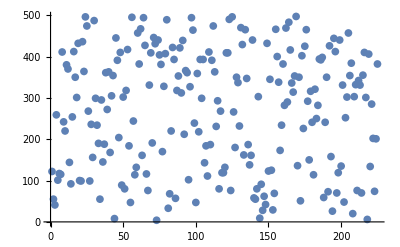
```mathematica
Cases[InputForm[-Graphics-],_Real]
```

{}

```mathematica
estring
```

{{72,125,96,55,75,71,64,88,128,44,50,95,127,55,68},{121,48,74,119,51,104,68,116,71,62,66,57,65,70,90},{78,79,100,111,84,69,105,39,55,41,58,87,74,45,52},{81,94,61,75,98,114,43,57,107,111,52,128,38,77,54},{66,107,126,37,95,103,48,57,65,123,73,47,80,38,93}}

```mathematica
estring//MatrixForm
```

(72 | 125 | 96 | 55 | 75 | 71 | 64 | 88 | 128 | 44 | 50 | 95 | 127 | 55 | 68
121 | 48 | 74 | 119 | 51 | 104 | 68 | 116 | 71 | 62 | 66 | 57 | 65 | 70 | 90
78 | 79 | 100 | 111 | 84 | 69 | 105 | 39 | 55 | 41 | 58 | 87 | 74 | 45 | 52
81 | 94 | 61 | 75 | 98 | 114 | 43 | 57 | 107 | 111 | 52 | 128 | 38 | 77 | 54
66 | 107 | 126 | 37 | 95 | 103 | 48 | 57 | 65 | 123 | 73 | 47 | 80 | 38 | 93)

```mathematica
Partition[ToCharacterCode["g/.:}.80yN"],4]//MatrixForm
```

(103 | 47 | 46 | 58
125 | 128 | 121 | 78)

```mathematica
stringtrans2//MatrixForm
```

(117 | 36 | 118 | 82 | 94
86 | 33 | 121 | 89 | 122
112 | 111 | 111 | 82 | 37
100 | 116 | 35 | 75 | 48
111 | 49 | 81 | 55 | 88
88 | 89 | 64 | 85 | 81
73 | 57 | 48 | 121 | 96
117 | 80 | 85 | 118 | 56
89 | 60 | 36 | 64 | 57
117 | 38 | 116 | 46 | 106
61 | 35 | 82 | 96 | 124
100 | 92 | 50 | 65 | 86
104 | 73 | 128 | 87 | 38
87 | 50 | 97 | 37 | 79
111 | 97 | 51 | 78 | 78)

```mathematica
stringtrans
```

{72,105,44,32,109,121,32,110,97,109,101,32,105,115,32,82,97,121,109,111,110,100,32,89,117,97,110,46,32,73,32,97,109,32,111,118,101,114,97,99,104,105,101,118,105,110,103,32,97,110,100,32,97,32,119,114,101,115,116,108,101,114,46,32,58,41,32,32,32,32,32,32,32,32,32}

```mathematica
Flatten[Transpose[Mod[dkey.(estring-32),97]+32]]
```

Dot::dotsh: Tensors {{1, 15, 83, 47, 64, 15, 76, 31, 82, 59, 29, 93, 53, 80, 6}, {18, 61, 10, 69, 50, 94, 11, 42, 45, 37, 9, 10, 81, 4, 66}, {71, 48, 23, 80, 64, 64, 25, 84, 35, 38, 25, 32, 36, 25, 94}, {85, 33, 4, 82, 13, 92, 76, 23, 80, 85, 6, 30, 23, 64, 30}, {3, 85, 31, 84, 50, 51, 19, 96, 84, 93, 5, 7, 52, 20, 85}, {85, 82, 32, 43, 57, 76, 74, 93, 93, 12, 54, 75, 77, 36, 83}, « 3 », {8, 73, 73, 43, 46, 8, 34, 13, 20, 32, 91, 29, 57, 59, 58}, {61, 75, 1, 9, 55, 61, 50, 37, 39, 41, 53, 83, 13, 12, 38}, {76, 90, 18, 29, 20, 50, 54, 41, 56, 76, 26, 86, 46, 20, 67}, {83, 14, 74, 90, 3, 40, 61, 50, 82, 55, 37, 25, 59, 47, 85}, {82, 18, 41, 19, 68, 77, 84, 24, 51, 83, 92, 72, 79, 58, 5}, {6, 27, 24, 77, 52, 95, 60, 44, 55, 77, 21, 29, 17, 11, 57}} and {{40, 93, 64, 23, 43, 39, 32, 56, 96, 12, 18, 63, 95, 23, 36}, {89, 16, 42, 87, 19, 72, 36, 84, 39, 30, 34, 25, 33, 38, 58}, {46, 47, 68, 79, 52, 37, 73, 7, 23, 9, 26, 55, 42, 13, 20}, {49, 62, 29, 43, 66, 82, 11, 25, 75, 79, 20, 96, 6, 45, 22}, {34, 75, 94, 5, 63, 71, 16, 25, 33, 91, 41, 15, 48, 6, 61}} have incompatible shapes.

Transpose[32+Mod[{{1,15,83,47,64,15,76,31,82,59,29,93,53,80,6},{18,61,10,69,50,94,11,42,45,37,9,10,81,4,66},{71,48,23,80,64,64,25,84,35,38,25,32,36,25,94},{85,33,4,82,13,92,76,23,80,85,6,30,23,64,30},{3,85,31,84,50,51,19,96,84,93,5,7,52,20,85},{85,82,32,43,57,76,74,93,93,12,54,75,77,36,83},{69,74,74,30,21,73,58,3,43,49,13,77,86,61,90},{6,13,6,53,73,89,4,3,16,84,68,35,39,20,96},{67,45,86,83,62,3,32,18,40,60,15,38,0,30,33},{8,73,73,43,46,8,34,13,20,32,91,29,57,59,58},{61,75,1,9,55,61,50,37,39,41,53,83,13,12,38},{76,90,18,29,20,50,54,41,56,76,26,86,46,20,67},{83,14,74,90,3,40,61,50,82,55,37,25,59,47,85},{82,18,41,19,68,77,84,24,51,83,92,72,79,58,5},{6,27,24,77,52,95,60,44,55,77,21,29,17,11,57}}.{{40,93,64,23,43,39,32,56,96,12,18,63,95,23,36},{89,16,42,87,19,72,36,84,39,30,34,25,33,38,58},{46,47,68,79,52,37,73,7,23,9,26,55,42,13,20},{49,62,29,43,66,82,11,25,75,79,20,96,6,45,22},{34,75,94,5,63,71,16,25,33,91,41,15,48,6,61}},97]]

```mathematica
Transpose[Partition[ToCharacterCode["7TlT{EwZ"],4]]//MatrixForm
```

(55 | 123
84 | 69
108 | 119
84 | 90)

```mathematica
dkey//MatrixForm
```

(1 | 15 | 83 | 47 | 64 | 15 | 76 | 31 | 82 | 59 | 29 | 93 | 53 | 80 | 6
18 | 61 | 10 | 69 | 50 | 94 | 11 | 42 | 45 | 37 | 9 | 10 | 81 | 4 | 66
71 | 48 | 23 | 80 | 64 | 64 | 25 | 84 | 35 | 38 | 25 | 32 | 36 | 25 | 94
85 | 33 | 4 | 82 | 13 | 92 | 76 | 23 | 80 | 85 | 6 | 30 | 23 | 64 | 30
3 | 85 | 31 | 84 | 50 | 51 | 19 | 96 | 84 | 93 | 5 | 7 | 52 | 20 | 85
85 | 82 | 32 | 43 | 57 | 76 | 74 | 93 | 93 | 12 | 54 | 75 | 77 | 36 | 83
69 | 74 | 74 | 30 | 21 | 73 | 58 | 3 | 43 | 49 | 13 | 77 | 86 | 61 | 90
6 | 13 | 6 | 53 | 73 | 89 | 4 | 3 | 16 | 84 | 68 | 35 | 39 | 20 | 96
67 | 45 | 86 | 83 | 62 | 3 | 32 | 18 | 40 | 60 | 15 | 38 | 0 | 30 | 33
8 | 73 | 73 | 43 | 46 | 8 | 34 | 13 | 20 | 32 | 91 | 29 | 57 | 59 | 58
61 | 75 | 1 | 9 | 55 | 61 | 50 | 37 | 39 | 41 | 53 | 83 | 13 | 12 | 38
76 | 90 | 18 | 29 | 20 | 50 | 54 | 41 | 56 | 76 | 26 | 86 | 46 | 20 | 67
83 | 14 | 74 | 90 | 3 | 40 | 61 | 50 | 82 | 55 | 37 | 25 | 59 | 47 | 85
82 | 18 | 41 | 19 | 68 | 77 | 84 | 24 | 51 | 83 | 92 | 72 | 79 | 58 | 5
6 | 27 | 24 | 77 | 52 | 95 | 60 | 44 | 55 | 77 | 21 | 29 | 17 | 11 | 57)

```mathematica
a
```

-7

```mathematica
encryption//MatrixForm
```

(330 | 176 | 150 | 341 | 398 | 167 | 491 | 2 | 379 | 184 | 255 | 43 | 22 | 197 | 209
420 | 334 | 6 | 195 | 328 | 128 | 304 | 295 | 248 | 312 | 389 | 375 | 435 | 404 | 152
459 | 256 | 87 | 233 | 75 | 15 | 398 | 266 | 138 | 254 | 482 | 373 | 386 | 185 | 284
446 | 399 | 120 | 113 | 346 | 328 | 304 | 464 | 147 | 36 | 238 | 290 | 474 | 427 | 315
335 | 189 | 326 | 432 | 418 | 307 | 176 | 91 | 310 | 58 | 384 | 77 | 128 | 133 | 337
18 | 346 | 159 | 18 | 166 | 140 | 325 | 333 | 239 | 13 | 421 | 425 | 10 | 184 | 321
454 | 355 | 210 | 334 | 334 | 488 | 215 | 163 | 392 | 313 | 66 | 220 | 124 | 273 | 319
65 | 74 | 70 | 188 | 178 | 7 | 40 | 21 | 451 | 236 | 413 | 230 | 468 | 497 | 238
398 | 90 | 481 | 40 | 149 | 321 | 225 | 253 | 304 | 382 | 169 | 341 | 496 | 236 | 398
142 | 424 | 134 | 279 | 216 | 283 | 281 | 443 | 414 | 135 | 233 | 276 | 168 | 341 | 379
259 | 475 | 97 | 387 | 316 | 355 | 498 | 157 | 162 | 215 | 231 | 182 | 212 | 485 | 232
240 | 448 | 359 | 490 | 416 | 209 | 224 | 356 | 401 | 457 | 394 | 199 | 351 | 35 | 462
299 | 162 | 466 | 116 | 395 | 94 | 76 | 395 | 200 | 264 | 134 | 15 | 358 | 247 | 258
338 | 204 | 101 | 371 | 29 | 149 | 290 | 134 | 37 | 35 | 384 | 270 | 66 | 132 | 114
372 | 289 | 309 | 392 | 241 | 27 | 129 | 33 | 407 | 219 | 323 | 473 | 362 | 195 | 395)

```mathematica
Mod[385,95]
```

5

```mathematica
estring//MatrixForm
```

(72 | 125 | 96 | 55 | 75 | 71 | 64 | 88 | 128 | 44 | 50 | 95 | 127 | 55 | 68
121 | 48 | 74 | 119 | 51 | 104 | 68 | 116 | 71 | 62 | 66 | 57 | 65 | 70 | 90
78 | 79 | 100 | 111 | 84 | 69 | 105 | 39 | 55 | 41 | 58 | 87 | 74 | 45 | 52
81 | 94 | 61 | 75 | 98 | 114 | 43 | 57 | 107 | 111 | 52 | 128 | 38 | 77 | 54
66 | 107 | 126 | 37 | 95 | 103 | 48 | 57 | 65 | 123 | 73 | 47 | 80 | 38 | 93)

```mathematica
Mod[{{79,48,34,28},
{32,64,67,73},
{41,33,35,90},
{84,92,16,9}}.(estring-32),95]+32
```

Dot::dotsh: Tensors {{79, 48, 34, 28}, {32, 64, 67, 73}, {41, 33, 35, 90}, {84, 92, 16, 9}} and {{40, 93, 64, 23, 43, 39, 32, 56, 96, 12, 18, 63, 95, 23, 36}, {89, 16, 42, 87, 19, 72, 36, 84, 39, 30, 34, 25, 33, 38, 58}, {46, 47, 68, 79, 52, 37, 73, 7, 23, 9, 26, 55, 42, 13, 20}, {49, 62, 29, 43, 66, 82, 11, 25, 75, 79, 20, 96, 6, 45, 22}, {34, 75, 94, 5, 63, 71, 16, 25, 33, 91, 41, 15, 48, 6, 61}} have incompatible shapes.

32+Mod[{{79,48,34,28},{32,64,67,73},{41,33,35,90},{84,92,16,9}}.{{40,93,64,23,43,39,32,56,96,12,18,63,95,23,36},{89,16,42,87,19,72,36,84,39,30,34,25,33,38,58},{46,47,68,79,52,37,73,7,23,9,26,55,42,13,20},{49,62,29,43,66,82,11,25,75,79,20,96,6,45,22},{34,75,94,5,63,71,16,25,33,91,41,15,48,6,61}},95]

```mathematica
encryption//MatrixForm
```

(330 | 176 | 150 | 341 | 398 | 167 | 491 | 2 | 379 | 184 | 255 | 43 | 22 | 197 | 209
420 | 334 | 6 | 195 | 328 | 128 | 304 | 295 | 248 | 312 | 389 | 375 | 435 | 404 | 152
459 | 256 | 87 | 233 | 75 | 15 | 398 | 266 | 138 | 254 | 482 | 373 | 386 | 185 | 284
446 | 399 | 120 | 113 | 346 | 328 | 304 | 464 | 147 | 36 | 238 | 290 | 474 | 427 | 315
335 | 189 | 326 | 432 | 418 | 307 | 176 | 91 | 310 | 58 | 384 | 77 | 128 | 133 | 337
18 | 346 | 159 | 18 | 166 | 140 | 325 | 333 | 239 | 13 | 421 | 425 | 10 | 184 | 321
454 | 355 | 210 | 334 | 334 | 488 | 215 | 163 | 392 | 313 | 66 | 220 | 124 | 273 | 319
65 | 74 | 70 | 188 | 178 | 7 | 40 | 21 | 451 | 236 | 413 | 230 | 468 | 497 | 238
398 | 90 | 481 | 40 | 149 | 321 | 225 | 253 | 304 | 382 | 169 | 341 | 496 | 236 | 398
142 | 424 | 134 | 279 | 216 | 283 | 281 | 443 | 414 | 135 | 233 | 276 | 168 | 341 | 379
259 | 475 | 97 | 387 | 316 | 355 | 498 | 157 | 162 | 215 | 231 | 182 | 212 | 485 | 232
240 | 448 | 359 | 490 | 416 | 209 | 224 | 356 | 401 | 457 | 394 | 199 | 351 | 35 | 462
299 | 162 | 466 | 116 | 395 | 94 | 76 | 395 | 200 | 264 | 134 | 15 | 358 | 247 | 258
338 | 204 | 101 | 371 | 29 | 149 | 290 | 134 | 37 | 35 | 384 | 270 | 66 | 132 | 114
372 | 289 | 309 | 392 | 241 | 27 | 129 | 33 | 407 | 219 | 323 | 473 | 362 | 195 | 395)